## Cryptography

### PowerMod[a,b,c]≡a^b(mod m)

```mathematica
PowerMod[2,10,37]
```

25

```mathematica
PowerMod[2,1,37]
```

2

```mathematica
PowerMod[2,-1,37]
```

19

### PowerModList[a,s/r,m]

#### ={x| x^r≡a^s(mod m)}

```mathematica
PowerModList[3,1/2,11]
```

{5,6}

#### 模11二次剩余

```mathematica
p=11;
Table[{i,PowerModList[i,1/2,p]},{i,1,p-1,1}]//MatrixForm
p=.
```

(1 | {1,10}
2 | {}
3 | {5,6}
4 | {2,9}
5 | {4,7}
6 | {}
7 | {}
8 | {}
9 | {3,8}
10 | {})

### PolynomialMod[poly,m]

#### 多项式poly模m的剩余多项式

```mathematica
PolynomialMod[(1+3x)^5,11]
```

1+4 x+2 x^2+6 x^3+9 x^4+x^5

```mathematica
PolynomialMod[(2+3x)^7,x^3-101x+37]
```

-888321661+2388894762 x+89307252 x^2

### BitXor

#### XOR/^

```mathematica
ArrayPlot[Table[Boole[BitXor[i,j]==i+j-10],{i,0,255},{j,0,255}]]
```

-Graphics-

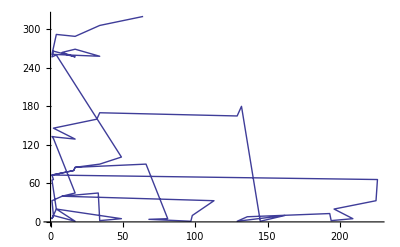

```mathematica
ListLinePlot[Table[{BitAnd[11i,5i],BitAnd[7i,5i]},{i,64}]]
```

```mathematica
IntegerDigits
```

```mathematica
Hex2Bin[x__]:=IntegerDigits[FromDigits[IntegerDigits@x,16],2]
```

```mathematica
Hex2Bin[57]
```

{1,0,1,0,1,1,1}